```mathematica
SetDirectory[NotebookDirectory[]]
<<KnotTheory`
```

/Users/dj/CLionProjects/c-flypes

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
Export["knot_txt_files/knot_4_1.txt",PD[Knot[4,1]]]
```

KnotTheory::loading: Loading precomputed data in PD4Knots`.

knot_txt_files/knot_4_1.txt

```mathematica
Export["knot_txt_files/knot_6_1.txt",PD[Knot[6,1]]]
```

knot_txt_files/knot_6_1.txt

```mathematica
Export["knot_txt_files/knot_15_70.txt",PD[Knot[15,Alternating,70]]]
```

knot_txt_files/knot_15_70.txt

```mathematica
Export["knot_txt_files/knot_16_1.txt",PD[Knot[16,Alternating,1]]]
```

KnotTheory::loading: Loading precomputed data in KnotTheory/16A.dts.

KnotTheory::credits: The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005.

knot_txt_files/knot_16_1.txt

```mathematica
Length@GetAllFlypesFromPD[PD@Knot[6,1]]
```

20

```mathematica
Length@GetAllFlypesFromPD[PD@Knot[15,Alternating,70]]
```

54

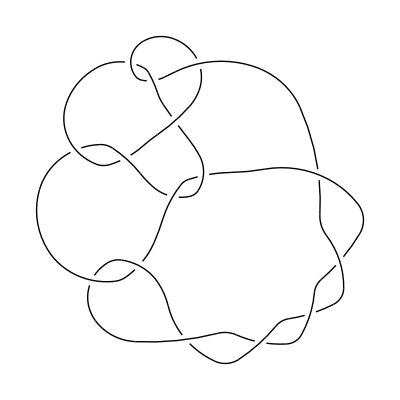

```mathematica
DrawPD[PD@Knot[15,Alternating,70],{Gap->0.03}]
```

```mathematica
Length/@GetAllFlypesFromPD[PD@Knot[6,1]][[All,1]]
```

{2,2,2,2,2,2,3,3,3,3,3,3,4,4,4,4,4,4,4,4}

```mathematica
Length[GetAllTanglesFromPD[PD@Knot[4,1]]]
```

2

```mathematica
Length[GetAllTanglesFromPD[PD@Knot[6,1]]]
```

12

```mathematica
Length[GetAllFlypesFromPD[PD@Knot[16,Alternating,1]]]
```

22

```mathematica
MatrixForm@({ParallelCheck[Knot[6,1],#⟦1⟧,#⟦2⟧],#⟦2⟧,#⟦1⟧}&/@GetAllFlypesFromPD[PD@Knot[6,1]])
```

(False | {11,6,12,7} | {{1,4,2,5},{5,12,6,1}}
True | {5,12,6,1} | {{7,10,8,11},{11,6,12,7}}
False | {1,4,2,5} | {{9,3,10,2},{3,9,4,8}}
False | {7,10,8,11} | {{9,3,10,2},{3,9,4,8}}
False | {1,4,2,5} | {{11,6,12,7},{5,12,6,1}}
False | {7,10,8,11} | {{11,6,12,7},{5,12,6,1}}
False | {7,10,8,11} | {{1,4,2,5},{5,12,6,1},{11,6,12,7}}
False | {7,10,8,11} | {{1,4,2,5},{9,3,10,2},{3,9,4,8}}
False | {5,12,6,1} | {{1,4,2,5},{9,3,10,2},{3,9,4,8}}
False | {1,4,2,5} | {{7,10,8,11},{3,9,4,8},{9,3,10,2}}
False | {11,6,12,7} | {{7,10,8,11},{3,9,4,8},{9,3,10,2}}
False | {1,4,2,5} | {{7,10,8,11},{11,6,12,7},{5,12,6,1}}
False | {7,10,8,11} | {{1,4,2,5},{5,12,6,1},{9,3,10,2},{3,9,4,8}}
False | {11,6,12,7} | {{1,4,2,5},{5,12,6,1},{9,3,10,2},{3,9,4,8}}
False | {3,9,4,8} | {{1,4,2,5},{5,12,6,1},{11,6,12,7},{7,10,8,11}}
False | {9,3,10,2} | {{1,4,2,5},{5,12,6,1},{11,6,12,7},{7,10,8,11}}
False | {5,12,6,1} | {{1,4,2,5},{9,3,10,2},{3,9,4,8},{7,10,8,11}}
False | {11,6,12,7} | {{1,4,2,5},{9,3,10,2},{3,9,4,8},{7,10,8,11}}
False | {1,4,2,5} | {{7,10,8,11},{11,6,12,7},{3,9,4,8},{9,3,10,2}}
True | {5,12,6,1} | {{7,10,8,11},{11,6,12,7},{3,9,4,8},{9,3,10,2}})